```mathematica
Get[FileNameJoin[{ParentDirectory[NotebookDirectory[], 3], "shared", "numerics", "constants.wl"}]];  (* TIDIED: shared canonical constants; supersedes the Constants cell below, which is kept for review. Delete the old cell + aliases once verified. *)
ħ = ℏ;
α[c_] := ℏΩ[c];
(* NOTE: old β[a,c] = π/(a c) differs by a factor 2 from shared ℏω00 = 2π/(a c); left unaliased -- verify which you intend. *)
```

# Lens-Shaped Quantum Dot

#### Constants

```mathematica
ħ=1.054571817*^-34;(*J·s*)
e=1.602176634*^-19;(*C*)
ε0=8.8541878128*^-12;(*F·m⁻.b9*)
kB=1.380649*^-23; (*J·K^-1*)
εr=12.8;(*GaAs dielectric constant*)
m₀=9.1093837015*^-31;(*kg*)
mₑ=0.067 m₀;
mₕ=0.45 m₀;
c0=2.99792458*^8;(*m/s,speed of light in vacuum*)

rB=4 π ε0 εr ħ^2/(mₑ e^2);(* ~10.2 nm for GaAs*)
ER=ħ^2/(2 mₑ rB^2);(* ~5.8 meV "electron Rydberg:"*)

Eg=1.424*e/ER;(*dimensionless gap in effective Rydbergs at 300 K*)
Ep=28.8*e/ER;(*dimensionless Kane energy in effective Rydbergs at 300 K*)

a=5;(*a in units rB*)
c=0.5;(*c in units rB*)
δ=0.01;(*softening length*)

w[a_, c_][r_]:=c Sqrt[1-r^2/a^2];
α[c_]:=π^2 /c^2 ;
β[a_, c_]:=π/(a c);
```

### Semi-Ellipsoid

```mathematica
a=5;c=1.5;
surf=ParametricPlot3D[
{a Sin[u] Cos[v],
a Sin[u] Sin[v],
c Cos[u]},
{u,0,Pi/2},{v,0,2 Pi},
PlotPoints->80,
Mesh->None,
PlotStyle->Directive[Blue,Opacity[0.4],Specularity[White,30]],
Lighting->"Neutral"];

bottom=ParametricPlot3D[
{a r Cos[t],a r Sin[t],0},
{r,0,1},{t,0,2 Pi},
Mesh->None,
PlotPoints->60,
PlotStyle->Directive[Blue,Opacity[0.4],Specularity[White,30]],
Lighting->"Neutral"];

rim=ParametricPlot3D[
{a Cos[t],a Sin[t],0},
{t,0,2 Pi},
PlotStyle->Directive[Black,Thin],PlotPoints->200];

axes=Graphics3D[
{Directive[Black,Opacity[1],Thick],
Arrow[{{0,0,0},{a,0,0}}],
Text[Style[HoldForm[a],FontFamily->"Times",FontSlant->Italic,FontSize->16],{a*0.8,-a*0.2,0}],
Arrow[{{0,0,0},{0,a,0}}],
Text[Style[HoldForm[a],FontFamily->"Times",FontSlant->Italic,FontSize->16],{a*0.15,a*0.8,0}],
Arrow[{{0,0,0},{0,0,c}}],
Text[Style[HoldForm[c],FontFamily->"Times",FontSlant->Italic,FontSize->16],{-a*0.1,0,c*0.7}]
}];

EllipsoidPlot=Show[
surf,bottom,rim,axes,
Boxed->False,
Axes->False,
PlotRange->{{-a,a},{-a,a},{0,c}},
ViewPoint->{1,-1.5,0.2},
ImageSize->500];

Export["G:/My Drive/Ասպիրանտուրա/Quantum-Dot/Graphs/Semi-ellipsoid.jpeg",EllipsoidPlot,"JPEG"];
```

## Single Particle

### States

```mathematica
ψnorm[a_, c_][nz_,nr_,m_]:=√(((β[a,c] nz)^(Abs[m]+1) Factorial[nr])/(π Gamma[nr+Abs[m]+1]));
ψz[a_, c_][nz_][z_,r_]:=√(2/(w[a, c][r])) Sin[(nz π z)/(w[a, c][r])];
ψr[a_, c_][nz_,nr_,m_][r_]:=Piecewise[{{r^Abs[m] Exp[-nz β[a, c] r^2/2]LaguerreL[nr,Abs[m],nz β[a,c] r^2], r>0}, {LaguerreL[nr,Abs[m],0], True}}]

ψ[a_, c_][nz_,nr_,m_][z_,r_,φ_]:=
ψnorm[a,c][nz,nr,m]*
Exp[ⅈ m φ]*
ψz[a,c][nz][z,r]*
ψr[a,c][nz,nr,m][r];
```

```mathematica
ClearAll[checkNorm];
checkNorm[{a_, c_},{nz_,nr_,m_}]:=
NIntegrate[
Module[{z=u w[a,c][r]},
Abs[ψ[a,c][nz,nr,m][z,r,φ]]^2  r w[a,c][r]
],
{r,0,a},{φ,0,2 π},{u,0,1},
AccuracyGoal->8,
PrecisionGoal->8
];
checkNorm[{a,c},{5,1,3}]
```

1.

### Energies

```mathematica
Energy[a_, c_][nz_,nr_,m_]:=α[c] nz^2+β [a,c]nz (2 nr+Abs[m]+1);

Ee[a_, c_][nz_,nr_,m_]:=Energy[a,c][nz,nr,m];
Eh[a_, c_][nz_,nr_,m_]:=(mₑ/mₕ) Energy[a,c][nz,nr,m];
```

### Plots

#### States

```mathematica
ClearAll[densityCash];
densityCash[nz_,nr_,m_]:=densityCash[nz,nr,m]=
DensityPlot[
(ψ[a, c][nz,nr,m][z,√(ρ^2+δ^2),0])^2,
{ρ,-a,a},{z,0,c},
Frame->False,
FrameTicks->None,
RegionFunction->Function[{ρ,z,ψ},z<=w[a,c][ρ]],
ColorFunction->"LakeColors",ColorFunctionScaling->True,
PlotRange->All,PlotPoints->100,PerformanceGoal->"Quality",
AspectRatio->0.1,
ImageSize->500];

ClearAll[ψPlot];
ψPlot[nz_,nr_,m_]:=Module[
{densityPlot,ρPlot,zPlot},
densityPlot=densityCash[nz,nr,m];

ρPlot = Plot[(ψr[a, c][nz,nr,m][Abs[ρ]])^2,{ρ,-a,a},PlotRange->All,
Axes->False,PlotStyle->{Thickness[0.002],Darker[Blue]},
AspectRatio->0.1,ImageSize->500];

zPlot=Plot[(ψz[a, c][nz][z,0])^2,{z,0,c},PlotRange->All,
Axes->False,PlotStyle->{Thickness[0.02],Darker[Blue]},
AspectRatio->1,ImageSize->500];
zPlot=Show[ImageRotate[zPlot,π/2],ImageSize->50];

Labeled[
GraphicsGrid[
{{,ρPlot},
{zPlot,densityPlot}},
Spacings->{0,0},
ImageSize->157*3
],
Row[{Style["n_z",FontFamily->"Times",FontSlant->Italic]," = ",nz,",  ",
Style["n_r",FontFamily->"Times",FontSlant->Italic]," = ",nr,",  ",
Style["m",FontFamily->"Times",FontSlant->Italic]," = ",m},
BaseStyle->{FontFamily->"Times",FontSize->10*3}]]
];
```

```mathematica
ψPlots=GraphicsGrid[
{{ψPlot[1,0,0],ψPlot[1,0,1],ψPlot[2,0,0]},
{ψPlot[1,1,0],ψPlot[1,0,2],ψPlot[2,0,1]}},
Spacings->{5*3,5*3},
ImageSize->470*3
]
Export["G:/My Drive/Ասպիրանտուրա/Quantum-Dot/Graphs/Psi.jpeg",ψPlots,"JPEG"];
```

-Graphics-

#### Energies

```mathematica
a=5;c=0.5;
aMin=2;aMax=5; 
cMin=0.7; cMax=2; 

states={{1,0,0},{1,0,1},{1,1,0},{2,0,0},{2,0,1},{2,1,0}};
labels=Row[{Style["n_z",FontFamily->"Times",FontSlant->Italic]," = ",#[[1]],",  ",
Style["n_r",FontFamily->"Times",FontSlant->Italic]," = ",#[[2]],",  ",
Style["m",FontFamily->"Times",FontSlant->Italic]," = ",#[[3]]},
BaseStyle->{FontFamily->"Times",FontSize->12}]&/@states;
styles=Thread@Directive[
ColorData[97,"ColorList"][[;;Length[states]]],
AbsoluteThickness[1.2]];
singleLegends=MapThread[LineLegend[{#1},{#2},LabelStyle->11]&,{styles,labels}];
legendGrid=Grid[Partition[singleLegends,3],Alignment->Center];
panelTag[ch_]:=Row[{Style[ch,Italic],")"},
BaseStyle->{FontFamily->"Times",FontSize->14}];

plotEc=Labeled[
Plot[
{Energy[a,c]@@states⟦1⟧, 
Energy[a,c]@@states⟦2⟧,
Energy[a,c]@@states⟦3⟧,
Energy[a,c]@@states⟦4⟧, 
Energy[a,c]@@states⟦5⟧,
Energy[a,c]@@states⟦6⟧},
{c,cMin,cMax},
PlotRange->{{cMin,cMax},{0,25}},
PlotStyle->styles,
Frame->True,
FrameLabel->{Row[{Style["c",Italic],", ",Subscript[Style["r",Italic],"B"]},BaseStyle->{FontFamily->"Times"}],
Rotate[Row[{Style["E_e",Italic],", Ry"},BaseStyle->{FontFamily->"Times"}],-90 Degree]},
ImageSize->500,
PlotTheme->"Scientific"
],
panelTag["a"],{Left,Top},Spacings->{0,0}
];

plotEa=Labeled[
Plot[
{Energy[a,c]@@states⟦1⟧, 
Energy[a,c]@@states⟦2⟧,
Energy[a,c]@@states⟦3⟧,
Energy[a,c]@@states⟦4⟧, 
Energy[a,c]@@states⟦5⟧,
Energy[a,c]@@states⟦6⟧},
{a,aMin,aMax},
PlotRange->All,
PlotStyle->styles,
Frame->True,
FrameLabel->{Row[{Style["a",Italic],", ",Subscript[Style["r",Italic],"B"]},BaseStyle->{FontFamily->"Times"}],
Rotate[Row[{Style["E_e",Italic],", Ry"},BaseStyle->{FontFamily->"Times"}],-90 Degree]},
ImageSize->500,
PlotTheme->"Scientific"
],
panelTag["b"],{Left,Top},Spacings->{0,0}
];

gridE=GraphicsGrid[{{plotEc,plotEa}},Spacings->{0.6,0.3}];
plotE=Column[{gridE, legendGrid},Alignment->Center]
Export["G:/My Drive/Ասպիրանտուրա/Quantum-Dot/Graphs/E_a=5_c=0.5.jpeg",plotE,"JPEG"];
```

-Graphics-
 |  | 
 |  |

## Exciton

### Interaction Energy

```mathematica
ρ[ze_,re_,zh_,rh_,Δφ_]:=√(re^2+rh^2-2 re rh Cos[Δφ]+(ze-zh)^2);
Vcoulomb[ze_,re_,zh_,rh_,Δφ_]:=1/(√(ρ[ze,re,zh,rh,Δφ]^2+δ^2));
CoulombIntegrand[a_,c_][eState_,hState_]:=
Function[{ue,re,uh,rh,Δφ},
Module[{ze=ue w[a,c][re],zh=uh w[a,c][rh],Ψe,Ψh},
Ψe=(ψ[a, c]@@eState)[ze,re,0];
Ψh=(ψ[a, c]@@hState)[zh,rh,Δφ];
2π*Abs[Ψe Ψh]^2* Vcoulomb[re,ze,rh,zh,Δφ]*
re w[a,c][re]*rh w[a,c][rh]
]
];
Ecoulomb[a_,c_][eState_,hState_]:=Ecoulomb[a,c][eState,hState]=
Module[{rmax=0.9,f},
f = CoulombIntegrand[a,c][eState,hState];
NIntegrate[
f[ue,re,uh,rh,Δφ],
{ue,0,1},{re,0,a rmax},{uh,0,1},{rh,0,a rmax},{Δφ,0,2π},
Method->{"AdaptiveQuasiMonteCarlo","BisectionDithering"->0,"MaxPoints"->10^6}
]
];

Eex0[a_,c_][eState_,hState_]:=Eg+Ee[a, c]@@eState+Eh[a, c]@@eState;
Eex[a_,c_][eState_,hState_]:=Eex0[a,c][eState,hState]-Ecoulomb[a,c][eState,hState];
```

#### Plots

```mathematica
States[nzMax_Integer?Positive,NMax_Integer?Positive]:=
Module[{mMax=NMax-1,nrMax=Floor[(NMax-1)/2]},
Flatten[
Table[If[2 nr+Abs[m]+1<=NMax,
{{nz,nr,m},{nz,nr,-m}},
Sequence@@{}],
{nz,1,nzMax},{nr,0,nrMax},{m,0,mMax}],
2]];
states=States[1,4];
```

```mathematica
a=5;c=0.5;
aMin=2;aMax=5; 
cMin=0.7; cMax=2; 

labels=Row[{Style["n_z",FontFamily->"Times",FontSlant->Italic]," = ",#[[1]][[1]],",  ",
Style["n_r",FontFamily->"Times",FontSlant->Italic]," = ",#[[1]][[2]],",  ",
Style["m",FontFamily->"Times",FontSlant->Italic]," = ",#[[1]][[3]]},
BaseStyle->{FontFamily->"Times",FontSize->9}]&/@states;
styles=Thread@Directive[
ColorData[97,"ColorList"][[;;Length[states]]],
AbsoluteThickness[1.2]];
singleLegends=MapThread[LineLegend[{#1},{#2},LabelStyle->11]&,{styles,labels}];
legendGrid=Grid[Partition[singleLegends,3],Alignment->Center,Spacings->{0,0}];
panelTag[ch_]:=Row[{Style[ch,Italic],")"},
BaseStyle->{FontFamily->"Times",FontSize->14}];
```

```mathematica
legendGrid
Export["G:/My Drive/Ասպիրանտուրա/Quantum-Dot/Graphs/Counlomb_legend.jpeg",legendGrid,"JPEG",ImageResolution->300];
```

|  | 
 |  |

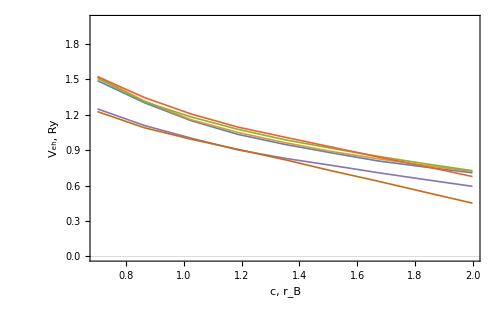

```mathematica
plotVc=
Plot[
{Ecoulomb[a,c][states⟦1⟧[[1]],states⟦1⟧[[2]]],
Ecoulomb[a,c][states⟦2⟧[[1]],states⟦2⟧[[2]]],
Ecoulomb[a,c][states⟦3⟧[[1]],states⟦3⟧[[2]]],
Ecoulomb[a,c][states⟦4⟧[[1]],states⟦4⟧[[2]]],
Ecoulomb[a,c][states⟦5⟧[[1]],states⟦5⟧[[2]]],
Ecoulomb[a,c][states⟦6⟧[[1]],states⟦6⟧[[2]]]},
{c,cMin,cMax},
PlotRange->{{cMin,cMax},{0,2}},
PlotStyle->styles,
PlotPoints->2,
MaxRecursion->3,
PerformanceGoal->"Speed",
Frame->True,
FrameLabel->{Row[{Style["c",Italic],", ",Subscript[Style["r",Italic],"B"]},BaseStyle->{FontFamily->"Times",FontSize->10}],
Rotate[Row[{Style["V_eh",Italic],", Ry"},BaseStyle->{FontFamily->"Times",FontSize->10}],-90 Degree]},
ImageSize->500,
PlotTheme->"Scientific"
];
labeledPlotVc=Labeled[plotVc,panelTag["a"],{Left,Top},Spacings->{0,0},ImageSize->470/2/0.9]
Export["G:/My Drive/Ասպիրանտուրա/Quantum-Dot/Graphs/Counlomb_a.jpeg",labeledPlotVc,"JPEG",ImageResolution->300];
```

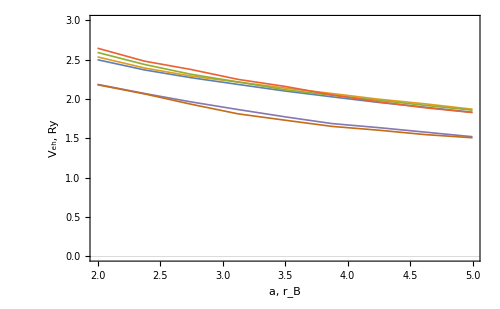

```mathematica
plotVa=
Plot[
{Ecoulomb[a,c][states⟦1⟧[[1]],states⟦1⟧[[2]]],
Ecoulomb[a,c][states⟦2⟧[[1]],states⟦2⟧[[2]]],
Ecoulomb[a,c][states⟦3⟧[[1]],states⟦3⟧[[2]]],
Ecoulomb[a,c][states⟦4⟧[[1]],states⟦4⟧[[2]]],
Ecoulomb[a,c][states⟦5⟧[[1]],states⟦5⟧[[2]]],
Ecoulomb[a,c][states⟦6⟧[[1]],states⟦6⟧[[2]]]},
{a,aMin,aMax},
PlotRange->{{aMin,aMax},{0,3}},
PlotStyle->styles,
PlotPoints->2,
MaxRecursion->3,
PerformanceGoal->"Speed",
Frame->True,
FrameLabel->{Row[{Style["a",Italic],", ",Subscript[Style["r",Italic],"B"]},BaseStyle->{FontFamily->"Times"}],
Rotate[Row[{Style["V_eh",Italic],", Ry"},BaseStyle->{FontFamily->"Times"}],-90 Degree]},
ImageSize->500,
PlotTheme->"Scientific"
];
labeledPlotVa=Labeled[plotVa,panelTag["b"],{Left,Top},Spacings->{0,0},ImageSize->470/2/0.9]
Export["G:/My Drive/Ասպիրանտուրա/Quantum-Dot/Graphs/Counlomb_b.jpeg",labeledPlotVa,"JPEG",ImageResolution->300];
```

### Lifetime

```mathematica
(*This section is in SI*)
τex0[a_,c_][{nz_,nr_,m_}]:=
Module[{E=Eex0[a,c][{nz,nr,m},{nz,nr,-m}]},
(2π ε0 mₑ c0^3 ħ^2)/(√εr e^2 (Ep*ER)(E*ER))];

τex[a_,c_][{nz_,nr_,m_}]:=
Module[{E=Eex[a,c][{nz,nr,m},{nz,nr,-m}]},
(2π ε0 mₑ c0^3 ħ^2)/(√εr e^2 (Ep*ER)(E*ER))];
```

#### Plots

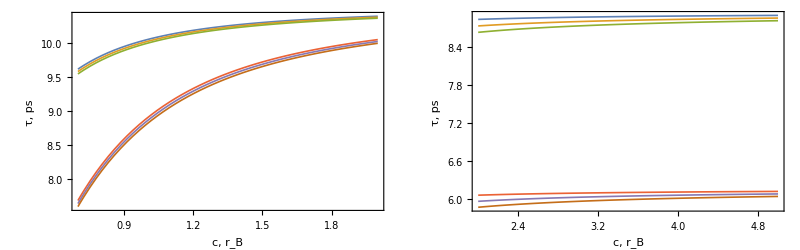
-Graphics-
 |  | 
 |  |

```mathematica
a=5;c=0.5;
aMin=2;aMax=5; 
cMin=0.7; cMax=2; 

states={{1,0,0},{1,0,1},{1,1,0},{2,0,0},{2,0,1},{2,1,0}};
labels=Style[
Row[{Subscript[n,z]," = ",#[[1]],", ",
Subscript[n,r]," = ",#[[2]],", ",
HoldForm[m]," = ",#[[3]]}],"InlineFormula"]&/@states;
styles=Thread@Directive[
ColorData[97,"ColorList"][[;;Length[states]]],
AbsoluteThickness[1.2]];
singleLegends=MapThread[LineLegend[{#1},{#2},LabelStyle->11]&,{styles,labels}];
legendGrid=Grid[Partition[singleLegends,3],Alignment->Center];

plotτc=Plot[
{τex0[a,c][states⟦1⟧]*10^12,
τex0[a,c][states⟦2⟧]*10^12,
τex0[a,c][states⟦3⟧]*10^12,
τex0[a,c][states⟦4⟧]*10^12,
τex0[a,c][states⟦5⟧]*10^12,
τex0[a,c][states⟦6⟧]*10^12},
{c,cMin,cMax},
PlotStyle->styles,
Frame->True,
FrameLabel->{Style["c, r_B",Italic],
Rotate[Style["τ, ps",Italic],-90 Degree]},
ImageSize->500,
PlotTheme->"Scientific"
];
plotτa=Plot[
{τex0[a,c][states⟦1⟧]*10^12,
τex0[a,c][states⟦2⟧]*10^12,
τex0[a,c][states⟦3⟧]*10^12,
τex0[a,c][states⟦4⟧]*10^12,
τex0[a,c][states⟦5⟧]*10^12,
τex0[a,c][states⟦6⟧]*10^12},
{a,aMin,aMax},
PlotStyle->styles,
Frame->True,
FrameLabel->{Style["c, r_B",Italic],
Rotate[Style["τ, ps",Italic],-90 Degree]},
ImageSize->500,
PlotTheme->"Scientific"
];
gridτ=GraphicsGrid[{{plotτc,plotτa}},Spacings->{0.6,0.3}];
plotτ=Column[{gridτ, legendGrid},Alignment->Center]
Export["G:/My Drive/Ասպիրանտուրա/Quantum-Dot/Graphs/tau_a=5_c=0.5.jpeg",plotτ,"JPEG"];
```

### Inter-band Absorption

```mathematica
γ=0.5*10^-3;

States[a_,c_][nzMax_Integer?Positive,NMax_Integer?Positive]:=
Module[{mMax=NMax-1,nrMax=Floor[(NMax-1)/2]},
Flatten[
Table[If[2 nr+Abs[m]+1<=NMax,
{{nz,nr,m},ER/e*Eex[a,c][{nz,nr,m},{nz,nr,-m}]},
Sequence@@{}],
{nz,1,nzMax},{nr,0,nrMax},{m,-mMax,mMax}],
2]];

LorentzPeak[ω0_,γ_]:=Function[{ω},(γ/π)/((ω-ω0)^2+γ^2)];
Absorption[states_]:=
Function[{ω},
Module[{terms},
terms=Table[LorentzPeak[states[[i]][[2]],γ][ω],{i,Length[states]}];
Total[terms]]];
```

```mathematica
states=States[a,c][1,7];
```

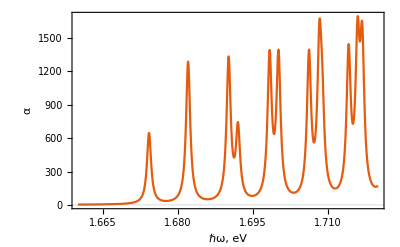

```mathematica
plotAbsorption=Labeled[
Plot[Absorption[states][ω],
{ω,1.66,1.72},
 PlotRange->{{1.66,1.72},{0,Automatic}},
Frame->True,
FrameLabel->{Row[{Style["ℏ",Italic],"ω, eV"},BaseStyle->{FontFamily->"Times"}],
Rotate[Style["α",FontFamily->"Times"],-90 Degree]},
FrameTicks->{{None,None},{Automatic,None}},
PlotTheme->"Scientific"],
panelTag["a"],{Left,Top},Spacings->{0,0},ImageSize->470/2/0.9*7/8.3
]
Export["G:/My Drive/Ասպիրանտուրա/Quantum-Dot/Graphs/PL_a.jpeg",plotAbsorption,"JPEG"];
```

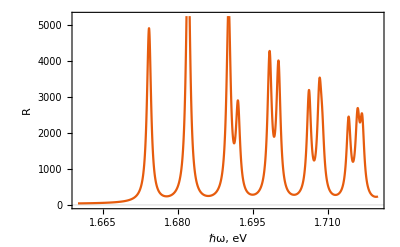

```mathematica
plotPhotoluminescence=Labeled[
Plot[Absorption[states][ω]*ω^2/Exp[(ω-1.7)/(300kB/e)],
{ω,1.66,1.72},
 PlotRange->{{1.66,1.72},{0,Automatic}},
Frame->True,
FrameLabel->{Row[{Style["ℏ",Italic],"ω, eV"},BaseStyle->{FontFamily->"Times"}],
Rotate[Style["R",Italic,FontFamily->"Times"],-90 Degree]},
FrameTicks->{{None,None},{Automatic,None}},
PlotTheme->"Scientific"],
panelTag["b"],{Left,Top},Spacings->{0,0},ImageSize->470/2/0.9*7/8.3
]
Export["G:/My Drive/Ասպիրանտուրա/Quantum-Dot/Graphs/PL_b.jpeg",plotPhotoluminescence,"JPEG"];
```

```mathematica
plotPL=GraphicsGrid[{{plotAbsorption,plotPhotoluminescence}},Spacings->{0.6,0.3}]
Export["G:/My Drive/Ասպիրանտուրա/Quantum-Dot/Graphs/PL_a=5_c=0.5.jpeg",plotPL,"JPEG"];
```

-Graphics-

### State Correlation

```mathematica
(*Doesn't work*)
```

```mathematica
ρeh[ρe_,φe_,ze_,ρh_,φh_,zh_]:=√((ze-zh)^2+ρe^2+ρh^2-2 ρe ρh Cos[φe-φh]);
ψex[a_, c_][nze_,nre_,me_,nzh_,nrh_,mh_,λ_][ρe_,φe_,ze_,ρh_,φh_,zh_]:=
ψ[a, c][nze,nre,me][ρe,φe,ze]*
ψ[a, c][nzh,nrh,mh][ρh,φh,zh]*
Exp[-λ ρeh[ρe,φe,ze,ρh,φh,zh]];
```

```mathematica
ClearAll[ρ,dρdre,dρdze,dρdrh,dρdzh,dρdφe,dρdφh]
ρ[re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=
√(re^2+rh^2-2 re rh Cos[Δφ]+(ze-zh)^2);

(*With φe=0 and φh=Δφ,we have φe-φh=-Δφ*)
dρdre[re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=(re-rh Cos[Δφ])/Max[ρ[re,ze,rh,zh,Δφ],$MachineEpsilon];

dρdze[re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=(ze-zh)/Max[ρ[re,ze,rh,zh,Δφ],$MachineEpsilon];

dρdrh[re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=(rh-re Cos[Δφ])/Max[ρ[re,ze,rh,zh,Δφ],$MachineEpsilon];

dρdzh[re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=-(ze-zh)/Max[ρ[re,ze,rh,zh,Δφ],$MachineEpsilon];

(*∂ρ/∂φe=(re rh sinΔφ)/ρ=-re rh sin(Δφ)/ρ ∂ρ/∂φh=-(re rh sinΔφ)/ρ=+re rh sin(Δφ)/ρ*)
dρdφe[re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=-(re rh Sin[Δφ])/Max[ρ[re,ze,rh,zh,Δφ],$MachineEpsilon];

dρdφh[re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=(re rh Sin[Δφ])/Max[ρ[re,ze,rh,zh,Δφ],$MachineEpsilon];

(*----------single-particle envelopes (as functions)----------*)
ClearAll[ψe,ψh]
ψe[a_,c_,nze_,nre_,me_][re_?NumericQ,φe_?NumericQ,ze_?NumericQ]:=ψ[a,c][nze,nre,me][re,φe,ze];

ψh[a_,c_,nzh_,nrh_,mh_][rh_?NumericQ,φh_?NumericQ,zh_?NumericQ]:=ψ[a,c][nzh,nrh,mh][rh,φh,zh];

(*analytic angular derivatives (faster& exact):∂/∂φ ψ=i m ψ*)
ClearAll[dψer,dψedz,dψedφ,dψhdr,dψhdz,dphdφ]
dψedr[a_,c_,nze_,nre_,me_][re_?NumericQ,φe_?NumericQ,ze_?NumericQ]:=dψedr[a,c,nze,nre,me][re,φe,ze]=Evaluate@D[ψ[a,c][nze,nre,me][ρ,φ,z],ρ]/. {ρ->re,φ->φe,z->ze};

dψedz[a_,c_,nze_,nre_,me_][re_?NumericQ,φe_?NumericQ,ze_?NumericQ]:=dψedz[a,c,nze,nre,me][re,φe,ze]=Evaluate@D[ψ[a,c][nze,nre,me][ρ,φ,z],z]/. {ρ->re,φ->φe,z->ze};

dψedφ[a_,c_,nze_,nre_,me_][re_?NumericQ,φe_?NumericQ,ze_?NumericQ]:=I me ψe[a,c,nze,nre,me][re,φe,ze];

dψhdr[a_,c_,nzh_,nrh_,mh_][rh_?NumericQ,φh_?NumericQ,zh_?NumericQ]:=dψhdr[a,c,nzh,nrh,mh][rh,φh,zh]=Evaluate@D[ψ[a,c][nzh,nrh,mh][ρ,φ,z],ρ]/. {ρ->rh,φ->φh,z->zh};

dψhdz[a_,c_,nzh_,nrh_,mh_][rh_?NumericQ,φh_?NumericQ,zh_?NumericQ]:=dψhdz[a,c,nzh,nrh,mh][rh,φh,zh]=Evaluate@D[ψ[a,c][nzh,nrh,mh][ρ,φ,z],z]/. {ρ->rh,φ->φh,z->zh};

dψhdφ[a_,c_,nzh_,nrh_,mh_][rh_?NumericQ,φh_?NumericQ,zh_?NumericQ]:=I mh ψh[a,c,nzh,nrh,mh][rh,φh,zh];

(*----------correlation factor and its derivatives----------*)
ClearAll[J,dJdre,dJdze,dJdrh,dJdzh,dJdφe,dJdφh]
J[λ_?NumericQ][re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=Exp[-λ ρ[re,ze,rh,zh,Δφ]];

dJdre[λ_?NumericQ][re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=-λ J[λ][re,ze,rh,zh,Δφ] dρdre[re,ze,rh,zh,Δφ];

dJdze[λ_?NumericQ][re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=-λ J[λ][re,ze,rh,zh,Δφ] dρdze[re,ze,rh,zh,Δφ];

dJdrh[λ_?NumericQ][re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=-λ J[λ][re,ze,rh,zh,Δφ] dρdrh[re,ze,rh,zh,Δφ];

dJdzh[λ_?NumericQ][re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=-λ J[λ][re,ze,rh,zh,Δφ] dρdzh[re,ze,rh,zh,Δφ];

dJdφe[λ_?NumericQ][re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=-λ J[λ][re,ze,rh,zh,Δφ] dρdφe[re,ze,rh,zh,Δφ];

dJdφh[λ_?NumericQ][re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=-λ J[λ][re,ze,rh,zh,Δφ] dρdφh[re,ze,rh,zh,Δφ];

(*----------gradient (product rule) and densities----------*)
ClearAll[dΨdre,dΨdze,dΨφe,dΨrh,dΨzh,dΨφh]
dΨdre[a_,c_,nze_,nre_,me_,nzh_,nrh_,mh_,λ_?NumericQ][re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=dψedr[a,c,nze,nre,me][re,0.,ze]*ψh[a,c,nzh,nrh,mh][rh,Δφ,zh]*J[λ][re,ze,rh,zh,Δφ]+ψe[a,c,nze,nre,me][re,0.,ze]*ψh[a,c,nzh,nrh,mh][rh,Δφ,zh]*dJdre[λ][re,ze,rh,zh,Δφ];

dΨdze[a_,c_,nze_,nre_,me_,nzh_,nrh_,mh_,λ_?NumericQ][re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=dψedz[a,c,nze,nre,me][re,0.,ze]*ψh[a,c,nzh,nrh,mh][rh,Δφ,zh]*J[λ][re,ze,rh,zh,Δφ]+ψe[a,c,nze,nre,me][re,0.,ze]*ψh[a,c,nzh,nrh,mh][rh,Δφ,zh]*dJdze[λ][re,ze,rh,zh,Δφ];

dΨφe[a_,c_,nze_,nre_,me_,nzh_,nrh_,mh_,λ_?NumericQ][re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=dψedφ[a,c,nze,nre,me][re,0.,ze]*ψh[a,c,nzh,nrh,mh][rh,Δφ,zh]*J[λ][re,ze,rh,zh,Δφ]+ψe[a,c,nze,nre,me][re,0.,ze]*ψh[a,c,nzh,nrh,mh][rh,Δφ,zh]*dJdφe[λ][re,ze,rh,zh,Δφ];

dΨrh[a_,c_,nze_,nre_,me_,nzh_,nrh_,mh_,λ_?NumericQ][re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=ψe[a,c,nze,nre,me][re,0.,ze]*dψhdr[a,c,nzh,nrh,mh][rh,Δφ,zh]*J[λ][re,ze,rh,zh,Δφ]+ψe[a,c,nze,nre,me][re,0.,ze]*ψh[a,c,nzh,nrh,mh][rh,Δφ,zh]*dJdzh[λ][re,ze,rh,zh,Δφ];

dΨzh[a_,c_,nze_,nre_,me_,nzh_,nrh_,mh_,λ_?NumericQ][re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=ψe[a,c,nze,nre,me][re,0.,ze]*dψhdz[a,c,nzh,nrh,mh][rh,Δφ,zh]*J[λ][re,ze,rh,zh,Δφ]+ψe[a,c,nze,nre,me][re,0.,ze]*ψh[a,c,nzh,nrh,mh][rh,Δφ,zh]*dJdzh[λ][re,ze,rh,zh,Δφ];

dΨφh[a_,c_,nze_,nre_,me_,nzh_,nrh_,mh_,λ_?NumericQ][re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=ψe[a,c,nze,nre,me][re,0.,ze]*dψhdφ[a,c,nzh,nrh,mh][rh,Δφ,zh]*J[λ][re,ze,rh,zh,Δφ]+ψe[a,c,nze,nre,me][re,0.,ze]*ψh[a,c,nzh,nrh,mh][rh,Δφ,zh]*dJdφh[λ][re,ze,rh,zh,Δφ];

(*densities*)
ClearAll[kinDensity,psiAbs2,coulDensity]
kinDensity[a_,c_,nze_,nre_,me_,nzh_,nrh_,mh_,λ_?NumericQ][re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=
Module[{eR,eZ,eΦ,hR,hZ,hΦ},
eR=dΨdre[a,c,nze,nre,me,nzh,nrh,mh,λ][re,ze,rh,zh,Δφ];
eZ=dΨdze[a,c,nze,nre,me,nzh,nrh,mh,λ][re,ze,rh,zh,Δφ];
eΦ=dΨφe[a,c,nze,nre,me,nzh,nrh,mh,λ][re,ze,rh,zh,Δφ];
hR=dΨdrh[a,c,nze,nre,me,nzh,nrh,mh,λ][re,ze,rh,zh,Δφ];
hZ=dΨdrh[a,c,nze,nre,me,nzh,nrh,mh,λ][re,ze,rh,zh,Δφ];
hΦ=dΨdrh[a,c,nze,nre,me,nzh,nrh,mh,λ][re,ze,rh,zh,Δφ];
Abs[eR]^2+Abs[eZ]^2+Abs[eΦ]^2/Max[re^2,$MachineEpsilon]+Abs[hR]^2+Abs[hZ]^2+Abs[hΦ]^2/Max[rh^2,$MachineEpsilon]];

psiAbs2[a_,c_,nze_,nre_,me_,nzh_,nrh_,mh_,λ_?NumericQ][re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=
Abs[ψe[a,c,nze,nre,me][re,0.,ze]*ψh[a,c,nzh,nrh,mh][rh,Δφ,zh]*J[λ][re,ze,rh,zh,Δφ]]^2;

coulDensity[a_,c_,nze_,nre_,me_,nzh_,nrh_,mh_,λ_?NumericQ][re_?NumericQ,ze_?NumericQ,rh_?NumericQ,zh_?NumericQ,Δφ_?NumericQ]:=
psiAbs2[a,c,nze,nre,me,nzh,nrh,mh,λ][re,ze,rh,zh,Δφ]/Max[ρ[re,ze,rh,zh,Δφ],$MachineEpsilon];

(*----------Rayleigh quotient (strict variational)----------*)
ClearAll[ExcitonEnergyStrict]
Options[ExcitonEnergyStrict]={AccuracyGoal->5,PrecisionGoal->5,MaxRecursion->4,Method->{"QuasiMonteCarlo","LatticeRule"},WorkingPrecision->MachinePrecision};

ExcitonEnergyStrict[a_?NumericQ,c_?NumericQ,nze_Integer,nre_Integer,me_Integer,nzh_Integer,nrh_Integer,mh_Integer,λ_?NumericQ,opts:OptionsPattern[]]:=Module[{num,den},num=2π NIntegrate[(kinDensity[a,c,nze,nre,me,nzh,nrh,mh,λ][re,ze,rh,zh,Δφ]-coulDensity[a,c,nze,nre,me,nzh,nrh,mh,λ][re,ze,rh,zh,Δφ])
 re rh,
{re,0,a},{ze,0,w[a,c][re]},
{rh,0,a},{zh,0,w[a,c][rh]},
{Δφ,0,2 Pi},
Evaluate@FilterRules[{opts},Options[NIntegrate]]];
den=2 Pi NIntegrate[psiAbs2[a,c,nze,nre,me,nzh,nrh,mh,λ][re,ze,rh,zh,Δφ] re rh,{re,0,a},{ze,0,w[a,c][re]},{rh,0,a},{zh,0,w[a,c][rh]},{Δφ,0,2 Pi},Evaluate@FilterRules[{opts},Options[NIntegrate]]];
num/den];

(*----------minimize over λ----------*)
ClearAll[FindOptimalLambdaStrict]
Options[FindOptimalLambdaStrict]=Join[Options[ExcitonEnergyStrict],{InitialGuess->0.8,MaxLambda->12.}];

FindOptimalLambdaStrict[a_?NumericQ,c_?NumericQ,nze_:1,nre_:0,me_:0,nzh_:1,nrh_:0,mh_:0,opts:OptionsPattern[]]:=
Module[
{init=OptionValue[InitialGuess],
maxL=OptionValue[MaxLambda],sol,energy},
energy[λ_?NumericQ]:=ExcitonEnergyStrict[a,c,nze,nre,me,nzh,nrh,mh,λ,FilterRules[{opts},Options[ExcitonEnergyStrict]]];
sol=NMinimize[{energy[λ],0<=λ<=maxL},{λ},
Method->"NelderMead",AccuracyGoal->6,PrecisionGoal->6];
<|"LambdaStar"->(λ/. Last[sol]),"EnergyMin"->First[sol],"Solution"->sol|>];
```

```mathematica
res=FindOptimalLambdaStrict[a,c,1,0,0,1,0,0,AccuracyGoal->5,PrecisionGoal->5,MaxRecursion->4];
res["LambdaStar"],res["EnergyMin"]
```

NMinimize::badopmtd: The method {AdaptiveNelderMead,MultiDirectionalSimplex,AdaptiveParameters→False} is not an optimization method.

NMinimize::nonopt: Options expected (instead of MultiDirectionalSimplex) beyond position 2 in Method→{NelderMead,MultiDirectionalSimplex}. An option must be a rule or a list of rules.